```mathematica
a = {{0, 1}, {0, 0}};
adag = Transpose[a]
```

{{0,0},{1,0}}

```mathematica
a1 = KroneckerProduct[a, IdentityMatrix[2]];
a1dag = Transpose[a1];
a2 = KroneckerProduct[IdentityMatrix[2], a];
a2dag = Transpose[a2];
```

{{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0}}

{{0,0,0,0},{1,0,0,0},{0,0,0,0},{0,0,1,0}}

```mathematica
H  = a1dag.a2 + a2dag.a1;
```

{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}}

```mathematica
ψ0 = 1/Sqrt[2]{0,1,I,0}
ψt = FullSimplify[ψ0.MatrixExp[-I*H*t]]
```

{0,1/(√2),ⅈ/(√2),0}

{0,(Cos[t]+Sin[t])/(√2),(ⅈ (Cos[t]-Sin[t]))/(√2),0}

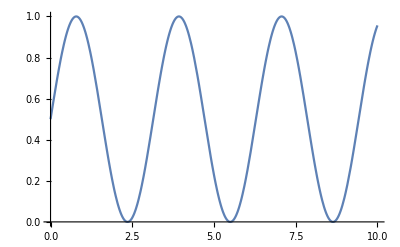

```mathematica
Plot[(Cos[t] + Sin[t])^2/2,{t, 0, 10}]
```

```mathematica
H = {{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}};
MatrixForm[H]
```

(0 | 1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Eigenvalues[H]
MatrixForm[Eigenvectors[H]]
```

{-1,-1,1,1}

(0 | 0 | -1 | 1
-1 | 1 | 0 | 0
0 | 0 | 1 | 1
1 | 1 | 0 | 0)

```mathematica
U = FullSimplify[MatrixExp[- I H t]];
Udag = FullSimplify[MatrixExp[I H t]];
Ubs = FullSimplify[MatrixExp[- I H Pi/4]];
Ubsdag = FullSimplify[MatrixExp[I H Pi/4]];
MatrixForm[U]
MatrixForm[Udag]
```

(Cos[t] | -ⅈ Sin[t] | 0 | 0
-ⅈ Sin[t] | Cos[t] | 0 | 0
0 | 0 | Cos[t] | -ⅈ Sin[t]
0 | 0 | -ⅈ Sin[t] | Cos[t])

(Cos[t] | ⅈ Sin[t] | 0 | 0
ⅈ Sin[t] | Cos[t] | 0 | 0
0 | 0 | Cos[t] | ⅈ Sin[t]
0 | 0 | ⅈ Sin[t] | Cos[t])

```mathematica
ψ0 = 1/2({1,0,1,0} + I {1,0,0,1} + I {0, 1,1, 0} - {0,1,0,1})
```

{1/2+ⅈ/2,-1/2+ⅈ/2,1/2+ⅈ/2,-1/2+ⅈ/2}

```mathematica
FullSimplify[Ubs.ψ0]
```

{(-1)^(1/4),0,(-1)^(1/4),0}